# Finding fixed points and the best responses graph of 2p2a games.

```mathematica
(*Check if the best player 2 uses the best strategy against player 1 and vice versa.*)
result[i_]:=
Module[{input = i},
(*Make assumptions on the Q-values and the game, based on the strategy.*)
assumptions = {
               If[input[[1]]==0, Q1000>Q1001, Q1000<Q1001],
               If[input[[2]]==0, Q1010>Q1011, Q1010<Q1011],
               If[input[[3]]==0, Q1100>Q1101, Q1100<Q1101],
               If[input[[4]]==0, Q1110>Q1111, Q1110<Q1111],
               If[input[[5]]==0, Q2000>Q2001, Q2000<Q2001],
               If[input[[6]]==0, Q2010>Q2011, Q2010<Q2011],
               If[input[[7]]==0, Q2100>Q2101, Q2100<Q2101],
               If[input[[8]]==0, Q2110>Q2111, Q2110<Q2111],
                t>r>p>s, 2r>t+s,0<d<1};

(*Make the Bellman equations.*)
Assuming[assumptions,
{
q1 = Simplify[Boole[Q2000>Q2001] (p+d*Q1000*Boole[Q1000>Q1001]+d*Q1001*Boole[Q1000<Q1001])+
                        Boole[Q2000<Q2001] (t+d*Q1010*Boole[Q1010>Q1011]+d*Q1011*Boole[Q1010<Q1011])],q2=  Simplify[Boole[Q2000>Q2001] (s+d*Q1100*Boole[Q1100>Q1101]+d*Q1101*Boole[Q1100<Q1101])+
                        Boole[Q2000<Q2001] (r+d*Q1110*Boole[Q1110>Q1111]+d*Q1111*Boole[Q1110<Q1111])],q3=  Simplify[Boole[Q2010>Q2011] (p+d*Q1000*Boole[Q1000>Q1001]+d*Q1001*Boole[Q1000<Q1001])+
                        Boole[Q2010<Q2011] (t+d*Q1010*Boole[Q1010>Q1011]+d*Q1011*Boole[Q1010<Q1011])],q4=  Simplify[Boole[Q2010>Q2011] (s+d*Q1100*Boole[Q1100>Q1101]+d*Q1101*Boole[Q1100<Q1101])+
                        Boole[Q2010<Q2011] (r+d*Q1110*Boole[Q1110>Q1111]+d*Q1111*Boole[Q1110<Q1111])],q5=  Simplify[Boole[Q2100>Q2101] (p+d*Q1000*Boole[Q1000>Q1001]+d*Q1001*Boole[Q1000<Q1001])+
                        Boole[Q2100<Q2101] (t+d*Q1010*Boole[Q1010>Q1011]+d*Q1011*Boole[Q1010<Q1011])],q6=  Simplify[Boole[Q2100>Q2101] (s+d*Q1100*Boole[Q1100>Q1101]+d*Q1101*Boole[Q1100<Q1101])+
                        Boole[Q2100<Q2101] (r+d*Q1110*Boole[Q1110>Q1111]+d*Q1111*Boole[Q1110<Q1111])],q7=  Simplify[Boole[Q2110>Q2111] (p+d*Q1000*Boole[Q1000>Q1001]+d*Q1001*Boole[Q1000<Q1001])+
                         Boole[Q2110<Q2111] (t+d*Q1010*Boole[Q1010>Q1011]+d*Q1011*Boole[Q1010<Q1011])],q8=  Simplify[Boole[Q2110>Q2111] (s+d*Q1100*Boole[Q1100>Q1101]+d*Q1101*Boole[Q1100<Q1101])+
                         Boole[Q2110<Q2111] (r+d*Q1110*Boole[Q1110>Q1111]+d*Q1111*Boole[Q1110<Q1111])],q9=  Simplify[Boole[Q1000>Q1001] (p+d*Q2000*Boole[Q2000>Q2001]+d*Q2001*Boole[Q2000<Q2001])+
                         Boole[Q1000<Q1001] (t+d*Q2100*Boole[Q2100>Q2101]+d*Q2011*Boole[Q2100<Q2101])],q10=Simplify[Boole[Q1000>Q1001] (s+d*Q2010*Boole[Q2010>Q2011]+d*Q2101*Boole[Q2010<Q2011])+
                         Boole[Q1000<Q1001] (r+d*Q2110*Boole[Q2110>Q2111]+d*Q2111*Boole[Q2110<Q2111])],q11=Simplify[Boole[Q1100>Q1101] (p+d*Q2000*Boole[Q2000>Q2001]+d*Q2001*Boole[Q2000<Q2001])+        
                         Boole[Q1100<Q1101] (t+d*Q2100*Boole[Q2100>Q2101]+d*Q2011*Boole[Q2100<Q2101])],q12=Simplify[Boole[Q1100>Q1101] (s+d*Q2010*Boole[Q2010>Q2011]+d*Q2101*Boole[Q2010<Q2011])+
                         Boole[Q1100<Q1101] (r+d*Q2110*Boole[Q2110>Q2111]+d*Q2111*Boole[Q2110<Q2111])],q13=Simplify[Boole[Q1010>Q1011] (p+d*Q2000*Boole[Q2000>Q2001]+d*Q2001*Boole[Q2000<Q2001])+
                         Boole[Q1010<Q1011] (t+d*Q2100*Boole[Q2100>Q2101]+d*Q2011*Boole[Q2100<Q2101])],q14=Simplify[Boole[Q1010>Q1011] (s+d*Q2010*Boole[Q2010>Q2011]+d*Q2101*Boole[Q2010<Q2011])+
                         Boole[Q1010<Q1011] (r+d*Q2110*Boole[Q2110>Q2111]+d*Q2111*Boole[Q2110<Q2111])],q15=Simplify[Boole[Q1110>Q1111] (p+d*Q2000*Boole[Q2000>Q2001]+d*Q2001*Boole[Q2000<Q2001])+
                         Boole[Q1110<Q1111] (t+d*Q2100*Boole[Q2100>Q2101]+d*Q2011*Boole[Q2100<Q2101])],q16=Simplify[Boole[Q1110>Q1111] (s+d*Q2010*Boole[Q2010>Q2011]+d*Q2101*Boole[Q2010<Q2011])+               
                         Boole[Q1110<Q1111] (r+d*Q2110*Boole[Q2110>Q2111]+d*Q2111*Boole[Q2110<Q2111])]
}];

sol1=Solve[{q1==Q1000, q2==Q1001, q3==Q1010, q4==Q1011, q5==Q1100, q6==Q1101, q7==Q1110, q8==Q1111},{Q1000, Q1001, Q1010, Q1011, Q1100, Q1101, Q1110, Q1111}];
formula1 = Assuming[assumptions,
 Simplify[Reduce[
  If[input[[1]]==0,Simplify[sol1[[1]][[1]][[2]] > sol1[[1]][[2]][[2]]], Simplify[sol1[[1]][[1]][[2]] < sol1[[1]][[2]][[2]]]] && 
If[input[[2]]==0,Simplify[sol1[[1]][[3]][[2]] > sol1[[1]][[4]][[2]]], Simplify[sol1[[1]][[3]][[2]] < sol1[[1]][[4]][[2]]]] && 
If[input[[3]]==0,Simplify[sol1[[1]][[5]][[2]] > sol1[[1]][[6]][[2]]], Simplify[sol1[[1]][[5]][[2]] < sol1[[1]][[6]][[2]]]] && 
If[input[[4]]==0,Simplify[sol1[[1]][[7]][[2]] > sol1[[1]][[8]][[2]]], Simplify[sol1[[1]][[7]][[2]] < sol1[[1]][[8]][[2]]]],d,Reals]]];

sol2=Solve[{q9==Q2000, q10==Q2001, q11==Q2100, q12==Q2101, q13==Q2010, q14==Q2011, q15==Q2110, q16==Q2111},{Q2000, Q2001, Q2010, Q2011, Q2100, Q2101, Q2110, Q2111}];
formula2 = Assuming[assumptions,
 Simplify[Reduce[
  If[input[[5]]==0,Simplify[sol2[[1]][[1]][[2]] > sol2[[1]][[2]][[2]]], Simplify[sol2[[1]][[1]][[2]] < sol2[[1]][[2]][[2]]]] && 
If[input[[7]]==0,Simplify[sol2[[1]][[3]][[2]] > sol2[[1]][[4]][[2]]], Simplify[sol2[[1]][[3]][[2]] < sol2[[1]][[4]][[2]]]] && 
If[input[[6]]==0,Simplify[sol2[[1]][[5]][[2]] > sol2[[1]][[6]][[2]]], Simplify[sol2[[1]][[5]][[2]] < sol2[[1]][[6]][[2]]]] && 
If[input[[8]]==0,Simplify[sol2[[1]][[7]][[2]] > sol2[[1]][[8]][[2]]], Simplify[sol2[[1]][[7]][[2]] < sol2[[1]][[8]][[2]]]],d,Reals]]];

Simplify[formula1 && formula2]
]

(* Create a list of the numbers 0 to 255 in binary, all with length 4. Example: [0,0,1,0],[1,1,0,1].*)
inputlist = {};
Do[AppendTo[inputlist, Join[ConstantArray[0,8-Length[IntegerDigits[i,2]]],IntegerDigits[i,2]]],{i,0,255}];

results = {};
Do[AppendTo[results, result[inputlist[[i]]]],{i,1,256}]
grid = {};
Do[AppendTo[grid, {inputlist[[i]],results[[i]]}],{i,1,256}];
Grid[grid,Frame->All]
```

{0,0,0,0,0,0,0,0} | True
{0,0,0,0,0,0,0,1} | False
{0,0,0,0,0,0,1,0} | False
{0,0,0,0,0,0,1,1} | False
{0,0,0,0,0,1,0,0} | False
{0,0,0,0,0,1,0,1} | False
{0,0,0,0,0,1,1,0} | False
{0,0,0,0,0,1,1,1} | False
{0,0,0,0,1,0,0,0} | False
{0,0,0,0,1,0,0,1} | False
{0,0,0,0,1,0,1,0} | False
{0,0,0,0,1,0,1,1} | False
{0,0,0,0,1,1,0,0} | False
{0,0,0,0,1,1,0,1} | False
{0,0,0,0,1,1,1,0} | False
{0,0,0,0,1,1,1,1} | False
{0,0,0,1,0,0,0,0} | False
{0,0,0,1,0,0,0,1} | r+d t>d p+t
{0,0,0,1,0,0,1,0} | False
{0,0,0,1,0,0,1,1} | False
{0,0,0,1,0,1,0,0} | False
{0,0,0,1,0,1,0,1} | False
{0,0,0,1,0,1,1,0} | False
{0,0,0,1,0,1,1,1} | False
{0,0,0,1,1,0,0,0} | False
{0,0,0,1,1,0,0,1} | False
{0,0,0,1,1,0,1,0} | False
{0,0,0,1,1,0,1,1} | False
{0,0,0,1,1,1,0,0} | False
{0,0,0,1,1,1,0,1} | False
{0,0,0,1,1,1,1,0} | False
{0,0,0,1,1,1,1,1} | False
{0,0,1,0,0,0,0,0} | False
{0,0,1,0,0,0,0,1} | False
{0,0,1,0,0,0,1,0} | False
{0,0,1,0,0,0,1,1} | False
{0,0,1,0,0,1,0,0} | False
{0,0,1,0,0,1,0,1} | False
{0,0,1,0,0,1,1,0} | False
{0,0,1,0,0,1,1,1} | False
{0,0,1,0,1,0,0,0} | False
{0,0,1,0,1,0,0,1} | False
{0,0,1,0,1,0,1,0} | False
{0,0,1,0,1,0,1,1} | False
{0,0,1,0,1,1,0,0} | False
{0,0,1,0,1,1,0,1} | False
{0,0,1,0,1,1,1,0} | False
{0,0,1,0,1,1,1,1} | False
{0,0,1,1,0,0,0,0} | False
{0,0,1,1,0,0,0,1} | False
{0,0,1,1,0,0,1,0} | False
{0,0,1,1,0,0,1,1} | False
{0,0,1,1,0,1,0,0} | False
{0,0,1,1,0,1,0,1} | False
{0,0,1,1,0,1,1,0} | False
{0,0,1,1,0,1,1,1} | False
{0,0,1,1,1,0,0,0} | False
{0,0,1,1,1,0,0,1} | False
{0,0,1,1,1,0,1,0} | False
{0,0,1,1,1,0,1,1} | False
{0,0,1,1,1,1,0,0} | False
{0,0,1,1,1,1,0,1} | False
{0,0,1,1,1,1,1,0} | False
{0,0,1,1,1,1,1,1} | False
{0,1,0,0,0,0,0,0} | False
{0,1,0,0,0,0,0,1} | False
{0,1,0,0,0,0,1,0} | False
{0,1,0,0,0,0,1,1} | False
{0,1,0,0,0,1,0,0} | False
{0,1,0,0,0,1,0,1} | False
{0,1,0,0,0,1,1,0} | False
{0,1,0,0,0,1,1,1} | False
{0,1,0,0,1,0,0,0} | False
{0,1,0,0,1,0,0,1} | False
{0,1,0,0,1,0,1,0} | False
{0,1,0,0,1,0,1,1} | False
{0,1,0,0,1,1,0,0} | False
{0,1,0,0,1,1,0,1} | False
{0,1,0,0,1,1,1,0} | False
{0,1,0,0,1,1,1,1} | False
{0,1,0,1,0,0,0,0} | False
{0,1,0,1,0,0,0,1} | False
{0,1,0,1,0,0,1,0} | False
{0,1,0,1,0,0,1,1} | False
{0,1,0,1,0,1,0,0} | False
{0,1,0,1,0,1,0,1} | False
{0,1,0,1,0,1,1,0} | False
{0,1,0,1,0,1,1,1} | False
{0,1,0,1,1,0,0,0} | False
{0,1,0,1,1,0,0,1} | False
{0,1,0,1,1,0,1,0} | False
{0,1,0,1,1,0,1,1} | False
{0,1,0,1,1,1,0,0} | False
{0,1,0,1,1,1,0,1} | False
{0,1,0,1,1,1,1,0} | False
{0,1,0,1,1,1,1,1} | False
{0,1,1,0,0,0,0,0} | False
{0,1,1,0,0,0,0,1} | False
{0,1,1,0,0,0,1,0} | False
{0,1,1,0,0,0,1,1} | False
{0,1,1,0,0,1,0,0} | False
{0,1,1,0,0,1,0,1} | False
{0,1,1,0,0,1,1,0} | False
{0,1,1,0,0,1,1,1} | False
{0,1,1,0,1,0,0,0} | False
{0,1,1,0,1,0,0,1} | False
{0,1,1,0,1,0,1,0} | False
{0,1,1,0,1,0,1,1} | False
{0,1,1,0,1,1,0,0} | False
{0,1,1,0,1,1,0,1} | False
{0,1,1,0,1,1,1,0} | False
{0,1,1,0,1,1,1,1} | False
{0,1,1,1,0,0,0,0} | False
{0,1,1,1,0,0,0,1} | False
{0,1,1,1,0,0,1,0} | False
{0,1,1,1,0,0,1,1} | False
{0,1,1,1,0,1,0,0} | False
{0,1,1,1,0,1,0,1} | False
{0,1,1,1,0,1,1,0} | False
{0,1,1,1,0,1,1,1} | False
{0,1,1,1,1,0,0,0} | False
{0,1,1,1,1,0,0,1} | False
{0,1,1,1,1,0,1,0} | False
{0,1,1,1,1,0,1,1} | False
{0,1,1,1,1,1,0,0} | False
{0,1,1,1,1,1,0,1} | False
{0,1,1,1,1,1,1,0} | False
{0,1,1,1,1,1,1,1} | False
{1,0,0,0,0,0,0,0} | False
{1,0,0,0,0,0,0,1} | False
{1,0,0,0,0,0,1,0} | False
{1,0,0,0,0,0,1,1} | False
{1,0,0,0,0,1,0,0} | False
{1,0,0,0,0,1,0,1} | False
{1,0,0,0,0,1,1,0} | False
{1,0,0,0,0,1,1,1} | False
{1,0,0,0,1,0,0,0} | False
{1,0,0,0,1,0,0,1} | False
{1,0,0,0,1,0,1,0} | False
{1,0,0,0,1,0,1,1} | False
{1,0,0,0,1,1,0,0} | False
{1,0,0,0,1,1,0,1} | False
{1,0,0,0,1,1,1,0} | False
{1,0,0,0,1,1,1,1} | False
{1,0,0,1,0,0,0,0} | False
{1,0,0,1,0,0,0,1} | False
{1,0,0,1,0,0,1,0} | False
{1,0,0,1,0,0,1,1} | False
{1,0,0,1,0,1,0,0} | False
{1,0,0,1,0,1,0,1} | False
{1,0,0,1,0,1,1,0} | False
{1,0,0,1,0,1,1,1} | False
{1,0,0,1,1,0,0,0} | False
{1,0,0,1,1,0,0,1} | r+d r>d p+t
{1,0,0,1,1,0,1,0} | False
{1,0,0,1,1,0,1,1} | False
{1,0,0,1,1,1,0,0} | False
{1,0,0,1,1,1,0,1} | False
{1,0,0,1,1,1,1,0} | False
{1,0,0,1,1,1,1,1} | False
{1,0,1,0,0,0,0,0} | False
{1,0,1,0,0,0,0,1} | False
{1,0,1,0,0,0,1,0} | False
{1,0,1,0,0,0,1,1} | False
{1,0,1,0,0,1,0,0} | False
{1,0,1,0,0,1,0,1} | False
{1,0,1,0,0,1,1,0} | False
{1,0,1,0,0,1,1,1} | False
{1,0,1,0,1,0,0,0} | False
{1,0,1,0,1,0,0,1} | False
{1,0,1,0,1,0,1,0} | False
{1,0,1,0,1,0,1,1} | False
{1,0,1,0,1,1,0,0} | False
{1,0,1,0,1,1,0,1} | False
{1,0,1,0,1,1,1,0} | False
{1,0,1,0,1,1,1,1} | False
{1,0,1,1,0,0,0,0} | False
{1,0,1,1,0,0,0,1} | False
{1,0,1,1,0,0,1,0} | False
{1,0,1,1,0,0,1,1} | False
{1,0,1,1,0,1,0,0} | False
{1,0,1,1,0,1,0,1} | False
{1,0,1,1,0,1,1,0} | False
{1,0,1,1,0,1,1,1} | False
{1,0,1,1,1,0,0,0} | False
{1,0,1,1,1,0,0,1} | False
{1,0,1,1,1,0,1,0} | False
{1,0,1,1,1,0,1,1} | False
{1,0,1,1,1,1,0,0} | False
{1,0,1,1,1,1,0,1} | False
{1,0,1,1,1,1,1,0} | False
{1,0,1,1,1,1,1,1} | False
{1,1,0,0,0,0,0,0} | False
{1,1,0,0,0,0,0,1} | False
{1,1,0,0,0,0,1,0} | False
{1,1,0,0,0,0,1,1} | False
{1,1,0,0,0,1,0,0} | False
{1,1,0,0,0,1,0,1} | False
{1,1,0,0,0,1,1,0} | False
{1,1,0,0,0,1,1,1} | False
{1,1,0,0,1,0,0,0} | False
{1,1,0,0,1,0,0,1} | False
{1,1,0,0,1,0,1,0} | False
{1,1,0,0,1,0,1,1} | False
{1,1,0,0,1,1,0,0} | False
{1,1,0,0,1,1,0,1} | False
{1,1,0,0,1,1,1,0} | False
{1,1,0,0,1,1,1,1} | False
{1,1,0,1,0,0,0,0} | False
{1,1,0,1,0,0,0,1} | False
{1,1,0,1,0,0,1,0} | False
{1,1,0,1,0,0,1,1} | False
{1,1,0,1,0,1,0,0} | False
{1,1,0,1,0,1,0,1} | False
{1,1,0,1,0,1,1,0} | False
{1,1,0,1,0,1,1,1} | False
{1,1,0,1,1,0,0,0} | False
{1,1,0,1,1,0,0,1} | False
{1,1,0,1,1,0,1,0} | False
{1,1,0,1,1,0,1,1} | False
{1,1,0,1,1,1,0,0} | False
{1,1,0,1,1,1,0,1} | False
{1,1,0,1,1,1,1,0} | False
{1,1,0,1,1,1,1,1} | False
{1,1,1,0,0,0,0,0} | False
{1,1,1,0,0,0,0,1} | False
{1,1,1,0,0,0,1,0} | False
{1,1,1,0,0,0,1,1} | False
{1,1,1,0,0,1,0,0} | False
{1,1,1,0,0,1,0,1} | False
{1,1,1,0,0,1,1,0} | False
{1,1,1,0,0,1,1,1} | False
{1,1,1,0,1,0,0,0} | False
{1,1,1,0,1,0,0,1} | False
{1,1,1,0,1,0,1,0} | False
{1,1,1,0,1,0,1,1} | False
{1,1,1,0,1,1,0,0} | False
{1,1,1,0,1,1,0,1} | False
{1,1,1,0,1,1,1,0} | False
{1,1,1,0,1,1,1,1} | False
{1,1,1,1,0,0,0,0} | False
{1,1,1,1,0,0,0,1} | False
{1,1,1,1,0,0,1,0} | False
{1,1,1,1,0,0,1,1} | False
{1,1,1,1,0,1,0,0} | False
{1,1,1,1,0,1,0,1} | False
{1,1,1,1,0,1,1,0} | False
{1,1,1,1,0,1,1,1} | False
{1,1,1,1,1,0,0,0} | False
{1,1,1,1,1,0,0,1} | False
{1,1,1,1,1,0,1,0} | False
{1,1,1,1,1,0,1,1} | False
{1,1,1,1,1,1,0,0} | False
{1,1,1,1,1,1,0,1} | False
{1,1,1,1,1,1,1,0} | False
{1,1,1,1,1,1,1,1} | False

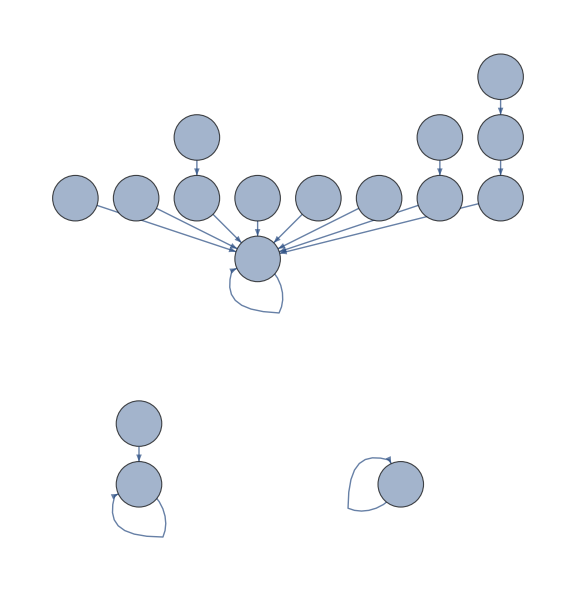

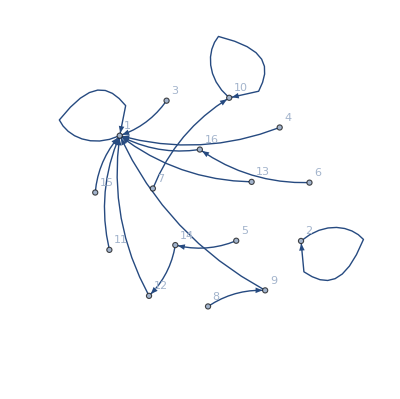

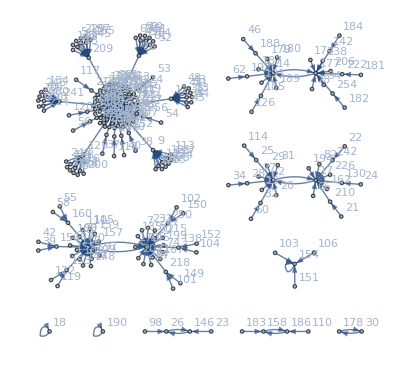

```mathematica
counter[i_,t_,r_,p_,s_,d_]:=
Module[{input = i},
assumptions = {
               If[input[[1]]==0, Q2000>Q2001, Q2000<Q2001],
               If[input[[2]]==0, Q2010>Q2011, Q2010<Q2011],
               If[input[[3]]==0, Q2100>Q2101, Q2100<Q2101],
               If[input[[4]]==0, Q2110>Q2111, Q2110<Q2111]
};
Assuming[assumptions,
{
q1=Simplify[Boole[Q2000>Q2001](p+d*Max[Q1000,Q1001])+Boole[Q2000<Q2001](t+d*Max[Q1010,Q1011])],q2=Simplify[Boole[Q2000>Q2001](s+d*Max[Q1100,Q1101])+Boole[Q2000<Q2001](r+d*Max[Q1110,Q1111])],q3=Simplify[Boole[Q2010>Q2011](p+d*Max[Q1000,Q1001])+Boole[Q2010<Q2011](t+d*Max[Q1010,Q1011])],q4=Simplify[Boole[Q2010>Q2011](s+d*Max[Q1100,Q1101])+Boole[Q2010<Q2011](r+d*Max[Q1110,Q1111])],q5=Simplify[Boole[Q2100>Q2101](p+d*Max[Q1000,Q1001])+Boole[Q2100<Q2101](t+d*Max[Q1010,Q1011])],q6=Simplify[Boole[Q2100>Q2101](s+d*Max[Q1100,Q1101])+Boole[Q2100<Q2101](r+d*Max[Q1110,Q1111])],q7=Simplify[Boole[Q2110>Q2111](p+d*Max[Q1000,Q1001])+Boole[Q2110<Q2111](t+d*Max[Q1010,Q1011])],q8=Simplify[Boole[Q2110>Q2111](s+d*Max[Q1100,Q1101])+Boole[Q2110<Q2111](r+d*Max[Q1110,Q1111])]
}];

sol=Solve[{q1==Q1000, q2==Q1001, q3==Q1010, q4==Q1011, q5==Q1100, q6==Q1101, q7==Q1110, q8==Q1111},
                        {Q1000, Q1001, Q1010, Q1011, Q1100, Q1101, Q1110, Q1111}];
output = {0,0,0,0};
output[[1]]=Boole[sol[[1]][[1]][[2]] < sol[[1]][[2]][[2]]];
output[[2]]=Boole[sol[[1]][[3]][[2]] < sol[[1]][[4]][[2]]];
output[[3]]=Boole[sol[[1]][[5]][[2]] < sol[[1]][[6]][[2]]];
output[[4]]=Boole[sol[[1]][[7]][[2]] < sol[[1]][[8]][[2]]];
output
];

(*All 16 strategies*)
strats = {};
Do[AppendTo[strats, Join[ConstantArray[0,4-Length[IntegerDigits[i,2]]],IntegerDigits[i,2]]],{i,0,15}];

(*Calculate the best responses*)
(*Change the values here*)
bestresps = {};
Do[AppendTo[bestresps, counter[{strats[[i]][[1]],strats[[i]][[3]],strats[[i]][[2]],strats[[i]][[4]]},3/2, 1, 0, -1/2, 8/10]],{i,1,16}]

(*All 256 strategy pairs*)
inputlist = {};
Do[AppendTo[inputlist, Join[ConstantArray[0,8-Length[IntegerDigits[i,2]]],IntegerDigits[i,2]]],{i,0,255}]

(*Find the best responses to the pairs*)
counterstrats = {};
Do[
p1 =FromDigits[{inputlist[[i]][[1]],inputlist[[i]][[3]],inputlist[[i]][[2]],inputlist[[i]][[4]]},2] + 1 ;
p2 = FromDigits[inputlist[[i]][[5;;8]],2] + 1 ;
AppendTo[counterstrats,Join[bestresps[[p2]],{bestresps[[p1]][[1]],bestresps[[p1]][[3]],bestresps[[p1]][[2]],bestresps[[p1]][[4]]}]];
,{i,1,256}];


(*Make the small graph*)
edges = {};
Do[AppendTo[edges, FromDigits[inputlist[[i]],2] + 1->FromDigits[bestresps[[i]],2] + 1],{i,1,16}];
Graph[edges, VertexLabels->Placed[Automatic,Center],VertexSize->.75, ImageSize->Large]

edges = {};
Do[Do[AppendTo[edges,i->j],{j,1,16}],{i,1,16}];
weights = ConstantArray[0,Length[edges]];
Do[Do[If[i==(FromDigits[inputlist[[i]],2] + 1 )&& j==(FromDigits[bestresps[[i]],2] + 1),weights[[(i-1)*16+j]]=1,weights[[(i-1)*16+j]]=0],{j,1,16}],{i,1,16}]
Graph[edges,VertexLabels->Automatic,EdgeStyle->Thread[edges->(Opacity[#]&/@weights)],ImageSize->Full]


(*Make the large graph*)
edges = {};
Do[AppendTo[edges, FromDigits[inputlist[[i]],2] + 1->FromDigits[counterstrats[[i]],2] + 1],{i,1,256}]
GraphPlot[edges, VertexLabels->Automatic, DirectedEdges->True, ImageSize->Full]
```